## LSTM

```mathematica
rescaledSubtractedTS=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\rescaledsubtractedTS.wxf"];
```

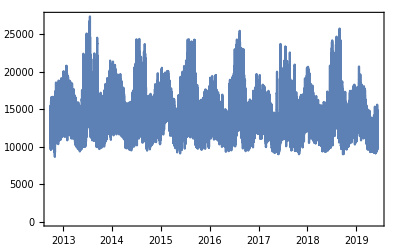

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
data=rescaledSubtractedTS//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,96,1];valuesp = values[[96;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,97}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
58680
```

```mathematica
Length@threaddata
```

57680

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
trainingdata[[;;1]]
```

{{{0.159085,0.118562,0.10918,0.106807,0.104909,0.116728,0.152632,0.225146,0.289792,0.319685,0.338191,0.35287,0.359959,0.35791,0.356961,0.348004,0.342932,0.345755,0.353725,0.365833,0.362265,0.330124,0.283926,0.223071,0.137913,0.12326,0.107858,0.117341,0.109798,0.0976672,0.103746,0.112823,0.170566,0.230599,0.271966,0.278188,0.282736,0.277933,0.26609,0.25616,0.250617,0.2566,0.273001,0.297125,0.306606,0.281995,0.244562,0.193141,0.120581,0.105957,0.0793112,0.0622618,0.0531212,0.0525585,0.061472,0.0743855,0.109394,0.165495,0.2166,0.24861,0.266367,0.273563,0.268372,0.261313,0.256788,0.26543,0.281747,0.30899,0.331724,0.301251,0.246141,0.182246,0.147933,0.0834182,0.0649467,0.0537673,0.0513277,0.0648874,0.109794,0.213246,0.275423,0.300498,0.317926,0.334367,0.341889,0.342278,0.343005,0.338339,0.334058,0.337598,0.350509,0.380523,0.399966,0.364491,0.301284,0.220552,0}}→0.220552}

```mathematica
columnHeads
```

```mathematica
mldata
```

$Aborted[]

```mathematica
rnn=NetChain[{
	LongShortTermMemoryLayer[20],
	LinearLayer[100],
	ElementwiseLayer[Ramp],
	60,
	Ramp,
	50,
	Ramp,1}]
```

NetChain[<>]

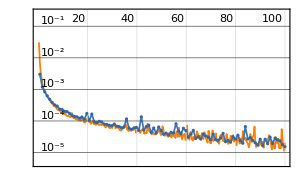
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainednet=NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→0.00110799|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{0.369093,0.37334,0.367965,0.35475,0.343098,0.338917,0.340734,0.358589,0.384605,0.397505,0.405578,0.377491,0.323889,0.256743,0.211822,0.188537,0.17249,0.164079,0.165224,0.166897,0.207014,0.296442,0.353349,0.369538,0.366807,0.349485,0.328841,0.319956,0.309879,0.296956,0.291862,0.305545,0.312741,0.335118,0.362622,0.348667,0.30274,0.240764,0.188206,0.183677,0.182704,0.191124,0.194581,0.200683,0.231884,0.294751,0.33124,0.321511,0.295134,0.265614,0.249684,0.235802,0.217807,0.229388,0.238462,0.244495,0.269115,0.290162,0.316543,0.304876,0.272053,0.224818,0.159459,0.150774,0.128844,0.118273,0.115618,0.122228,0.133473,0.170785,0.208757,0.23419,0.227264,0.203925,0.184213,0.178723,0.1853,0.184151,0.177411,0.198374,0.225001,0.249843,0.277329,0.268897,0.241725,0.202498,0.173308,0.130919,0.120008,0.122228,0.118563,0.122376,0.125927,0.145388,0.173981,0.215455,0}}→0.215455,{{0.132999,0.113477,0.109631,0.112344,0.131025,0.15343,0.209249,0.252979,0.256041,0.250144,0.256307,0.252906,0.241815,0.257404,0.249385,0.270205,0.296964,0.297775,0.300904,0.316309,0.310272,0.26756,0.225418,0.150583,0.150919,0.141981,0.139322,0.135898,0.133573,0.162153,0.231466,0.272505,0.272004,0.258995,0.24489,0.228464,0.211088,0.225494,0.229338,0.229583,0.228057,0.245916,0.270904,0.293894,0.295754,0.254209,0.194076,0.17287,0.109082,0.096383,0.0916914,0.0997525,0.104877,0.149673,0.214117,0.276394,0.306126,0.317819,0.321661,0.310038,0.296758,0.300435,0.298885,0.28391,0.275949,0.281013,0.298734,0.316542,0.314321,0.274055,0.214301,0.142526,0.124804,0.102386,0.108033,0.108296,0.125721,0.160199,0.227421,0.263461,0.25553,0.236812,0.231585,0.210341,0.21144,0.194013,0.178617,0.18421,0.207492,0.220467,0.240329,0.261807,0.270654,0.240083,0.192828,0.116481,0}}→0.116481}

```mathematica
trainednet[rsample[[2,1]]]
```

NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{0.132999,0.113477,0.109631,0.112344,0.131025,0.15343,0.209249,0.252979,0.256041,0.250144,0.256307,0.252906,0.241815,0.257404,0.249385,0.270205,0.296964,0.297775,0.300904,0.316309,0.310272,0.26756,0.225418,0.150583,0.150919,0.141981,0.139322,0.135898,0.133573,0.162153,0.231466,0.272505,0.272004,0.258995,0.24489,0.228464,0.211088,0.225494,0.229338,0.229583,0.228057,0.245916,0.270904,0.293894,0.295754,0.254209,0.194076,0.17287,0.109082,0.096383,0.0916914,0.0997525,0.104877,0.149673,0.214117,0.276394,0.306126,0.317819,0.321661,0.310038,0.296758,0.300435,0.298885,0.28391,0.275949,0.281013,0.298734,0.316542,0.314321,0.274055,0.214301,0.142526,0.124804,0.102386,0.108033,0.108296,0.125721,0.160199,0.227421,0.263461,0.25553,0.236812,0.231585,0.210341,0.21144,0.194013,0.178617,0.18421,0.207492,0.220467,0.240329,0.261807,0.270654,0.240083,0.192828,0.116481,0}}]

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
tvalues=Table[trainednet[testdata[[i,1]]],{i,1,Length@testdata}]
```

$Aborted[]

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainednet[#]}],1]&,testdata[[1,1]],100]
```

{0,195,NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{NetTrain Results
summary | ,,  batches:5700  rounds:100  time:56s  examples/s:82240
data | ,,  training examples:45000  validation examples:13585  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:1.56×10^-5
validation | ,,  loss:1.54×10^-5
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{0.254679,0.174088,0.193649,0.171725,0.169055,0.171057,85,0.361189,0.351966,0.331106,0.303687,0.257774,0}}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}]}
 |  |  |  |

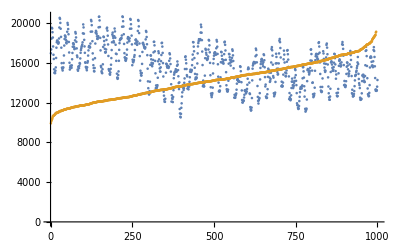

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```